{3,1.75,2.15,1,5,12,1000}

{40,0.05,2}

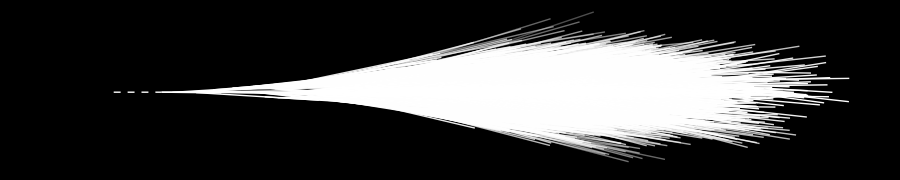

```mathematica
SeedRandom[3]
op={x,y};
p={op,ang,leng,gen};
PL={};(*particle list*)
OP[x_]:=PL⟦x,1⟧
ANG[x_]:=PL⟦x,2⟧
LEN[x_]:=PL⟦x,3⟧
GEN[x_]:=PL⟦x,4⟧
{angspread,minlen,maxlen,minnchi,maxnchi,genlimit,npart}={3,1.75,2.15,1,5,12,1000}

{a1,b1,c1}={40,0.05,2}
FF[x_]:=Sqrt[c1 b1-(x^2 b1)/a1]
InBound[f_]:=Module[{},
{fx,fy}=f;
If[Abs[fy]<FF[fx],
True,False]
]

GenChildren[tid_]:=Module[{j,nchild,op,ang,len,cop,cang,clen,gen,cgen},
If[tid<8,
nchild=2,
nchild=Random[Integer,{minnchi,maxnchi}]
];
op=OP[tid];
ang=ANG[tid];
len=LEN[tid];
gen=GEN[tid];
If[InBound[op],
For[j=0,j<nchild,j++,
cop=op+(RandomReal[]*len*{Cos[ang],Sin[ang]});
cang=ang+Random[Integer,{-angspread,angspread}]°;
clen=(maxlen-minlen)*RandomReal[]+minlen;
cgen=gen+1;
AppendTo[PL,{cop,cang,clen,cgen}]
]
]
]

pinit={{0,0},0.5°,1,1};
AppendTo[PL,pinit];
pinit={{0,0},-0.5°,1,1};
AppendTo[PL,pinit];

For[i=1,i≤npart,i++,
If[GEN[i]>genlimit,Print["Stopped due to GenLimit"];i=npart+20;Break];
GenChildren[i];
]
PL//TableForm;

GFXL={};
Clear[i];
For[i=1,i≤Length[PL],i++,
op=OP[i];
ang=ANG[i];
len=LEN[i];
{opx,opy}=op;
{op2x,op2y}=op+len*{Cos[ang],Sin[ang]};
op2={op2x,op2y};
line=If[i<3,
{White,Thin,Opacity[1-(opy*op2y*1.5)],Line[{op,op2}]},
{White,Thin,Opacity[1-(opy*op2y*1.5)],Line[{op,op2}]}
];
AppendTo[GFXL,line]
];
AppendTo[GFXL,{White,Dashed,Thick,Line[{{-0.8,0},{0,0}}]}];
pl=Plot[{FF[x],-FF[x]},{x,0,20},PlotRange->{-5,5},PlotStyle->{White,White}];
Showergfx=Show[Graphics[GFXL],PlotRange->All,AspectRatio->0.2,Frame->True,FrameStyle->White,Background->Black]
```

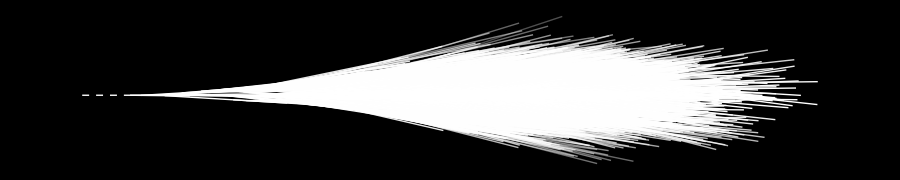

```mathematica
Showergfx=Show[Graphics[GFXL],PlotRange->All,AspectRatio->0.2,ImageSize->900,Background->Black]
```

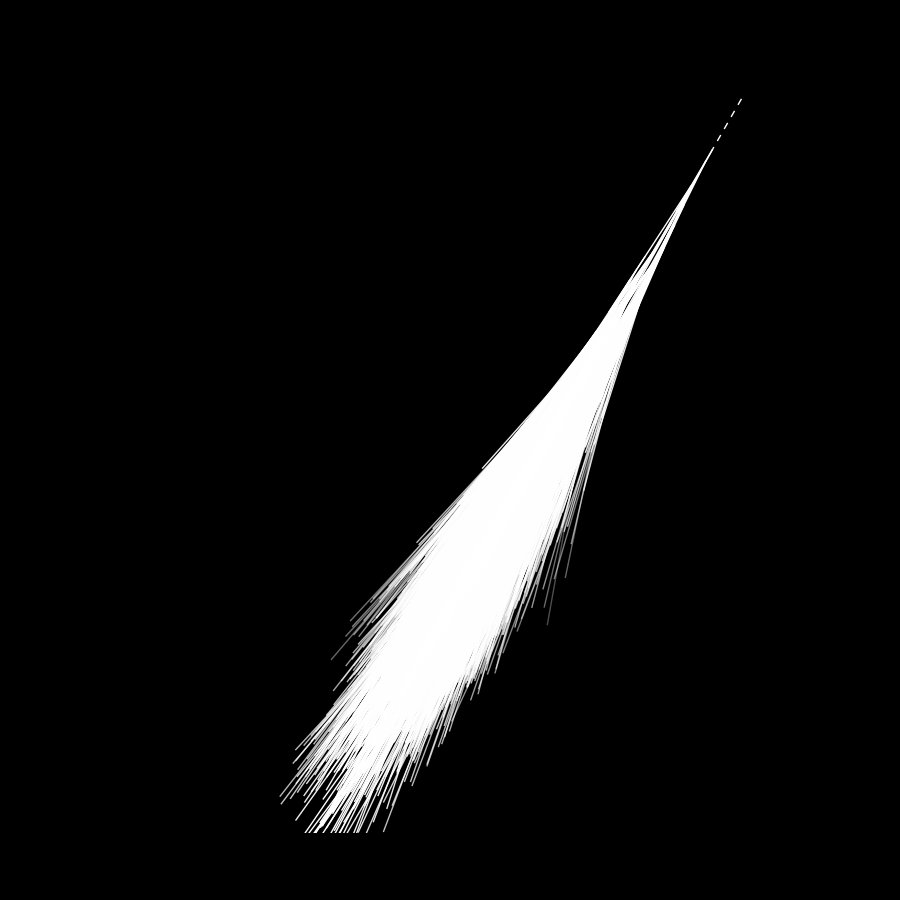

```mathematica
Showerfx[{x_,y_},ang_]:=Show[Graphics[Rotate[Translate[GFXL,{x,y}],ang,{x,y}]],PlotRange->All,AspectRatio->0.4,ImageSize->900,Background->Black]
Show[Showerfx[{0,10},-110°],PlotRange->{{-6,1},{0,11}},AspectRatio->1]
```

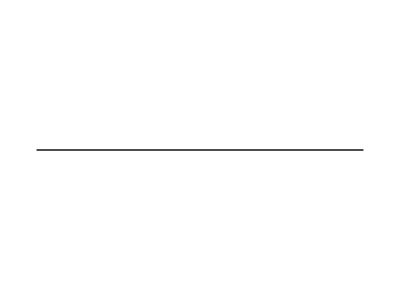

```mathematica
gnd={Black,Line[{{0,0},{6,0}}]};
tank={,};
Show[Graphics[{gnd}],PlotRange->All]
```